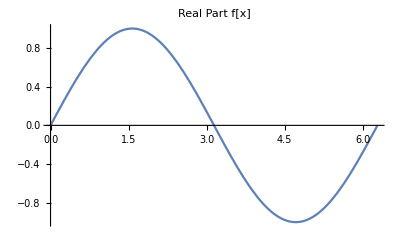

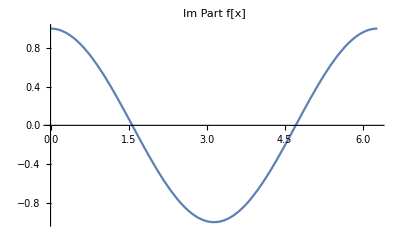

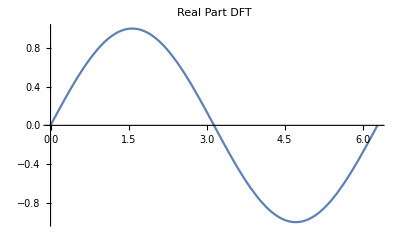

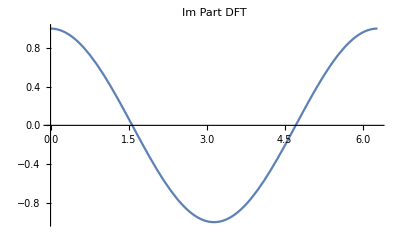

```mathematica
(* f is a complex-valued function defined on uniform partition of 0 to 2Pi.
Using Discrete Fourier Interpolation to determine fourier coefficients and numerically
verifying theorem from class stating that the size (using usual norm) of f evaluated at points along the partition and considered as an n-tuple in C^n is the same as the size (using semi-norm) of DF Interpolation of f*)

f[x_]:=Sin[x]+I*Cos[x];

n =5;
h = 2*Pi/n;
xvec = {};
For[i=0,i≤n-1,++i,
Subscript[x, i]=i*h;
AppendTo[xvec,Subscript[x, i]]
];

If[EvenQ[n],
Subscript[m, 0]= n/2;
Subscript[m, 1]=n/2,
Subscript[m, 0]=(n-1)/2;
Subscript[m, 1]=(n-1)/2
];

coef = {};
For[k=-Subscript[m, 0],k≤Subscript[m, 1]-1,++k,
Subscript[C, k]=(1/n)*∑_(i=0)^(n-1) f[Subscript[x, i]]*Exp[-I*k*Subscript[x, i]];
AppendTo[coef,Subscript[C, k]]
];

DFT[x_]:=∑_(k=-Subscript[m, 0])^(Subscript[m, 1]-1) Subscript[C, k] Exp[I*k*x]
Plot[Re[f[x]],{x, 0, 2*Pi},PlotLabel->"Real Part f[x]"]
Plot[Im[f[x]],{x,0,2*Pi},PlotLabel->"Im Part f[x]"]
Plot[Re[DFT[x]],{x,0,2*Pi},PlotLabel->"Real Part DFT"]
Plot[Im[DFT[x]],{x,0,2*Pi},PlotLabel->"Im Part DFT"]
```

```mathematica
N[Norm[f[xvec]],10]  (* comparing norm of f as n-tuple to semi-norm of DFInterpolation of f*)
```

2.236067977

```mathematica
N[Sqrt[n*∑_(k=-Subscript[m, 0])^(Subscript[m, 1]-1) Subscript[C, k]*Conjugate[Subscript[C, k]]],10]
```

2.236067977+0. ⅈ